```mathematica
f[x_]:=(4275)*((Sin[Pi*0.1*Sin[(x-4)/500]/(0.000546)]*(0.000546/(Pi*0.1*Sin[(x-4)/500])))^2)*(Cos[Pi*0.406*Sin[(x-4)/500]/0.000546]^2);
Table[f[x],{x,0,8,0.05}]
```

Fraunhofer Model for double slit and single slit: fit comparison with data and parameter optimization

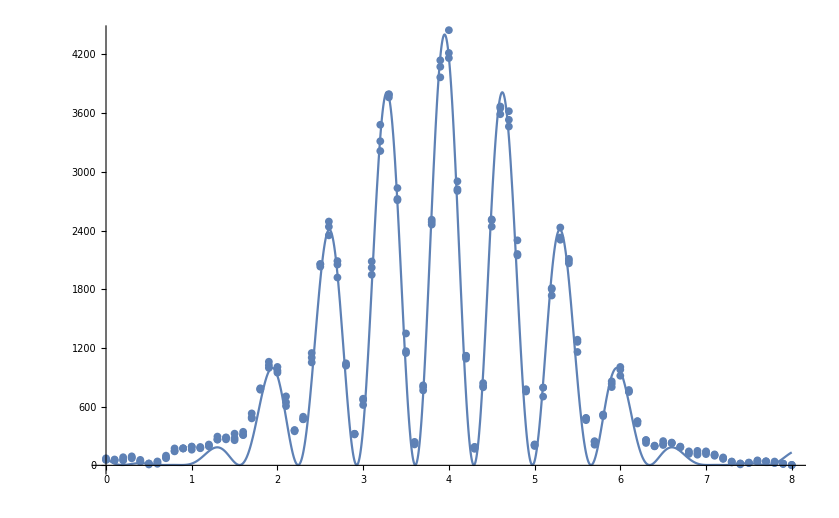

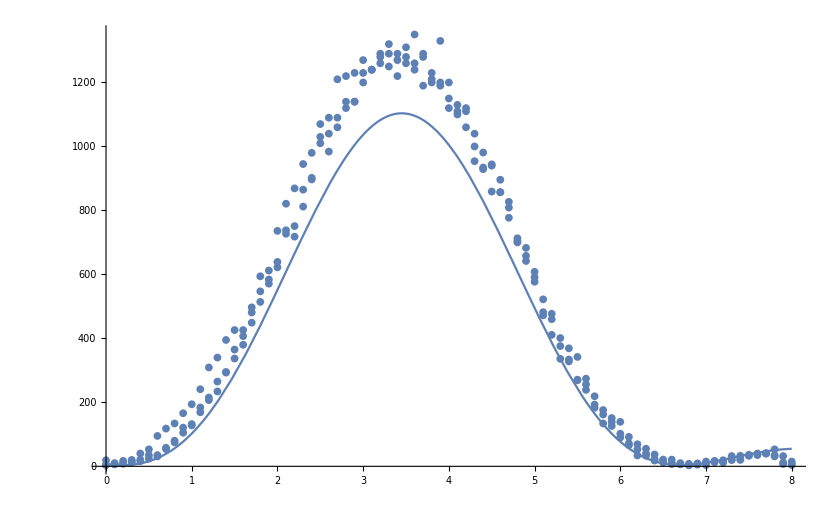

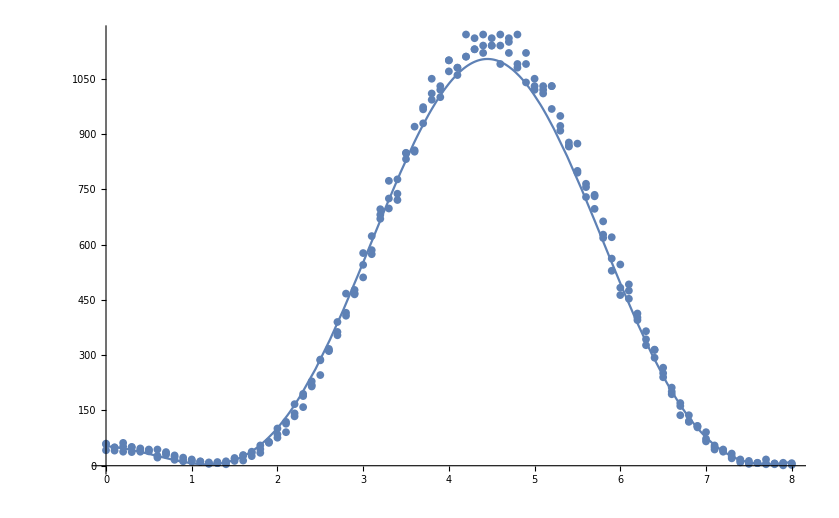

```mathematica
data2Slit = Import["/Users/iliparti/PhotonInterferenceLab/Analysis/4.45mmAll.csv"];
g[x_]:= I0*((Sin[Pi*a*Sin[(x-x0)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/D2])))^2)*(Cos[Pi*d*Sin[(x-x0)/D2]/lambda]^2)+c;
I0 = 4400;
a = 0.085;
d = 0.406;
lambda = 0.000555;
x0 = 3.95;
c = 3.6;
D1=338;
D2=500;
fit = Plot[g[x],{x,0,8}];
dataPlot2Slit = ListPlot[data2Slit,PlotMarkers->{Automatic,8}];
Show[fit,dataPlot2Slit]

dataFarSlit = Import["/Users/iliparti/PhotonInterferenceLab/Analysis/4mmAll.csv"];
h[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x1)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x1)/D2])))^2)+c;
x1 = 3.45;
fit2 = Plot[h[x],{x,0,8},PlotRange->All];
dataPlotFarSlit = ListPlot[dataFarSlit,PlotMarkers->{Automatic,8}];
Show[fit2,dataPlotFarSlit]

dataNearSlit = Import["/Users/iliparti/PhotonInterferenceLab/Analysis/5.9mmAll.csv"];
k[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x2)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x2)/D2])))^2)+c;
x2 = 4.45;
fit3 = Plot[k[x],{x,0,8},PlotRange->All];
dataPlotNearSlit = ListPlot[dataNearSlit,PlotMarkers->{Automatic,8}];
Show[fit3,dataPlotNearSlit]
```

Fresnel Model for double slit and single slit: fit comparison with data and parameter optimization

```mathematica
Clear[fresnel2]
```

```mathematica
i1[z_] := Exp[2*Pi*I*D1/lambda]*Exp[2*Pi*I*D2/lambda]*(Integrate[Exp[Pi*I*((x0-y)^2)/D1*lambda]*Exp[Pi*I*((y-z)^2)/D2*lambda],{y,x0+(d/2),x0+(d/2)+a}]);
i2[z_] := Exp[2*Pi*I*D1/lambda]*Exp[2*Pi*I*D2/lambda]*(Integrate[Exp[Pi*I*((x0-y)^2)/D1*lambda]*Exp[Pi*I*((y-z)^2)/D2*lambda],{y,x0-(d/2)-a,x0-(d/2)}]);
i[z_]:=Exp[2*Pi*I*D1/lambda]*Exp[2*Pi*I*D2/lambda]*(Integrate[Exp[Pi*I*((x0-y)^2)/D1*lambda]*Exp[Pi*I*((y-z)^2)/D2*lambda],{y,x0+(d/2),x0+(d/2)+a}]+Integrate[Exp[Pi*I*((x0-y)^2)/D1*lambda]*Exp[Pi*I*((y-z)^2)/D2*lambda],{y,x0-(d/2)-a,x0-(d/2)}]);
fresnel2[z_] := Re[i[z]*Conjugate[i[z]]];
fresnel[z_] :=Re[ i1[z]*Conjugate[i1[z]]+ i2[z]*Conjugate[i2[z]]];
fresnel2[2.5]
fresnel2[8]
```

0.0289

0.0289

```mathematica
Integrate[Exp[Pi*I*((x0-y)^2)/D1*lambda]*Exp[Pi*I*((y-z)^2)/D2*lambda],{y,x0+(d/2),x0+(d/2)+a}]
Integrate[Exp[Pi*I*((x0-y)^2)/D1*lambda]*Exp[Pi*I*((y-z)^2)/D2*lambda],{y,x0-(d/2)-a,x0-(d/2)}]
```

2.71828^(((0.-0.0000164371 ⅈ)+(0.+2.08065×10^-6 ⅈ) z) z) ((-213.13+213.116 ⅈ) Erfi[(0.00373456+0.00373456 ⅈ)-(0.000838606+0.000838606 ⅈ) z]+(213.13-213.116 ⅈ) Erfi[(0.00391129+0.00391129 ⅈ)-(0.000838606+0.000838606 ⅈ) z])

2.71828^(((0.-0.0000164371 ⅈ)+(0.+2.08065×10^-6 ⅈ) z) z) ((-213.13+213.116 ⅈ) Erfi[(0.0027137+0.0027137 ⅈ)-(0.000838606+0.000838606 ⅈ) z]+(213.13-213.116 ⅈ) Erfi[(0.00289043+0.00289043 ⅈ)-(0.000838606+0.000838606 ⅈ) z])

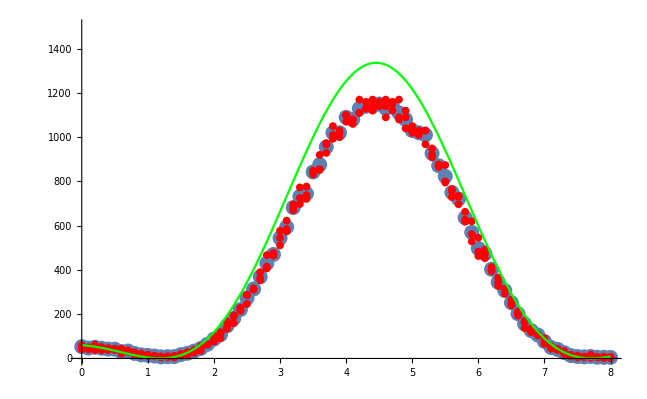

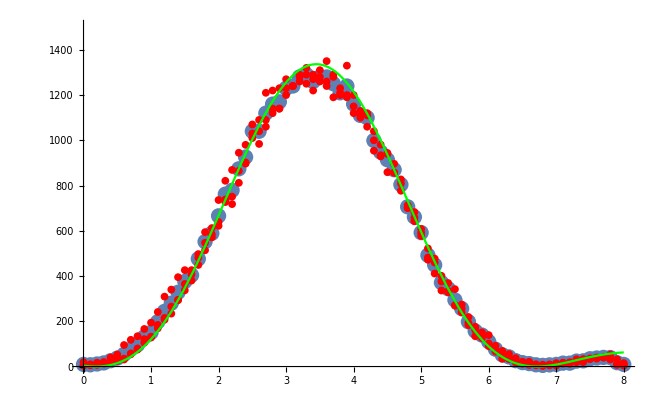

```mathematica
slit1[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0+(d/2)-(a/2),x0+(d/2)+(a/2)}]
s1[z_]:=42.044*I0*Re[slit1[z]*Conjugate[slit1[z]]]
slit2[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0-(d/2)-(a/2),x0-(d/2)+(a/2)}]
s2[z_]:=42.044*I0*Re[slit2[z]*Conjugate[slit2[z]]]
fitb=Plot[s1[z],{z,0,8},PlotStyle->Green];
fitc=Plot[s2[z],{z,0,8},PlotStyle->Green];
dataNearSlitAvg = Import["/Users/iliparti/PhotonInterferenceLab/Analysis/5.9mmAvg.csv"];
dataPlotNearSlitAvg = ListPlot[dataNearSlitAvg,PlotRange->{0,1500}];
dataPlotNearSlit = ListPlot[dataNearSlit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataFarSlitAvg = Import["/Users/iliparti/PhotonInterferenceLab/Analysis/4mmAvg.csv"];
dataPlotFarSlitAvg = ListPlot[dataFarSlitAvg,PlotRange->{0,1500}];
dataPlotFarSlit = ListPlot[dataFarSlit,PlotMarkers->{Automatic,8},PlotStyle->Red];
Show[dataPlotNearSlitAvg,dataPlotNearSlit,fitb]
Show[dataPlotFarSlitAvg,dataPlotFarSlit,fitc]
```

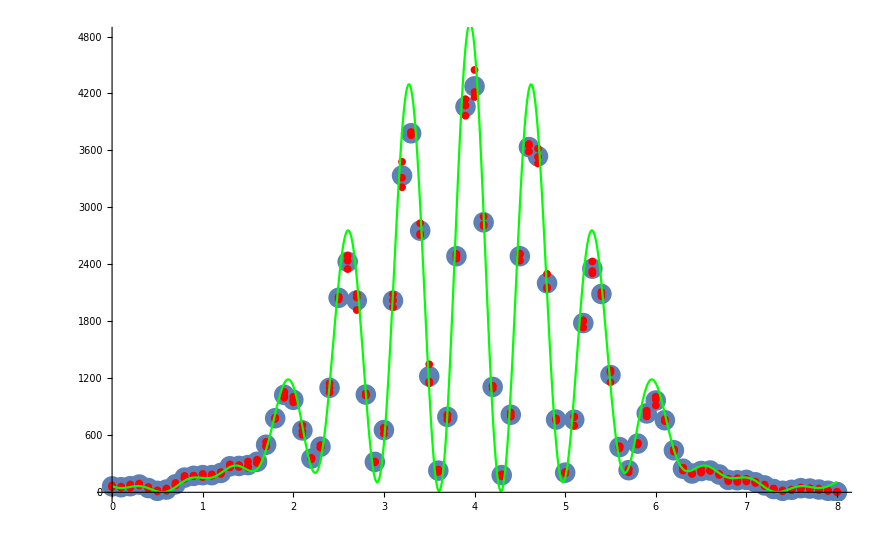

```mathematica
data2SlitAvg = Import["/Users/iliparti/PhotonInterferenceLab/Analysis/4.45mmAvg.csv"];
dataPlot2SlitAvg = ListPlot[data2SlitAvg,PlotRange->{0,4800}];
dataPlot2Slit = ListPlot[data2Slit,PlotMarkers->{Automatic,8},PlotStyle->Red];
slit[z_]:=42.044*I0*Re[(slit1[z]+slit2[z])*Conjugate[(slit1[z]+slit2[z])]]
fita=Plot[slit[z],{z,0,8},PlotStyle->Green];
Show[dataPlot2SlitAvg,dataPlot2Slit,fita]
```

```mathematica
slitdouble[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0+(d/2),x0+(d/2)+a}]+ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0-(d/2)-a,x0-(d/2)}]
slit[z_]:=40*I0*Re[slit[z]*Conjugate[slit[z]]]
fita=Plot[slit[z],{z,0,8}];
Show[fita,dataPlot2Slit]
```

Chi Square

```mathematica
justValuesDouble = Flatten[Import["/Users/iliparti/PhotonInterferenceLab/Analysis/just_values_double.csv"]];
justValuesFar = Flatten[Import["/Users/iliparti/PhotonInterferenceLab/Analysis/just_values_far.csv"]];
justValuesNear = Flatten[Import["/Users/iliparti/PhotonInterferenceLab/Analysis/just_values_near.csv"]];
```

```mathematica
redchisq[data_,dist_]:=Abs[Total[((data-dist)^2)/dist]/Mean[data]]
```

```mathematica
dataNearFres=Flatten[Table[s1[z],{z,0,8,.1}]];
dataFarFres=Flatten[Table[s2[z],{z,0,8,.1}]];
dataDoubleFres=Flatten[Table[slit[z],{z,0,8,.1}]];
```

```mathematica
redchisq[justValuesNear,dataNearFres]
```

4.4534

```mathematica
redchisq[justValuesFar,dataFarFres]
```

3.45065

```mathematica
redchisq[justValuesDouble,dataDoubleFres]
```

5.99359